```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/phy452-basicstatmech

### Problem 1.

Gamma[nu] PolyLog[nu,z]

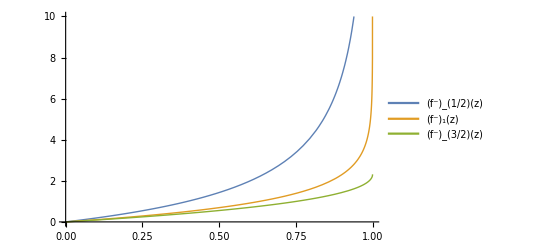

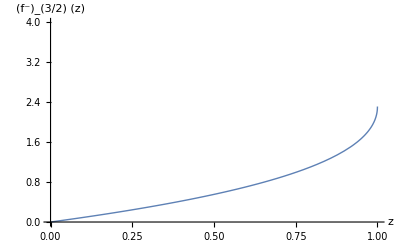

```mathematica
Clear[f, nu, x]
$Assumptions = nu > 0 ;
f[nu_, z_] = Integrate[ x^(nu -1)/(E^x/z - 1), {x, 0, Infinity}]

basicStatMechProblemSet7Problem1Fig1 = Module[{w},
w = {1/2, 1, 3/2} ;
Plot[
Evaluate[Map[ f[#, z] &, w]],
{z, 0, 1},
PlotRange -> {0, 10},
PlotStyle->Thick,
PlotLegends->Placed[
Map[ 
Row[{Subscript["f^-", Text[#]]//fs, Text["(z)" ]//fs}]&, w],
{Left, Top}
]
]
]
Plot[
f[3/2, z],
{z, 0, 1},
PlotRange -> {0, 4},
PlotStyle->Thick,
AxesLabel->{z, "(f^-)_(3/2)" Text["(z)"]}
]
```

### numerical calculations for problem set 7, p2.

```mathematica
Clear[t, kb, hbar]
t[n_, m_, kb_, hbar_] = (1/kb) (n/Zeta[3/2])^(2/3) 2 Pi hbar^2/m
hbar=1.05457173×10^(-34)  (* m^2 kg/s *)
kb = 1.3806488×10^(-23) (* m^2 kg s^-2 *)
t[n, m, kb, hbar]
t[1.88 10^28, 6.64 10^(-27), kb, hbar]
t[10^24, 1.443 10^(-25), kb, hbar]
Zeta[3/2] // N
```

(2 hbar^2 n^(2/3) π)/(kb m Zeta[3/2]^(2/3))

1.05457×10^-34

1.38065×10^-23

(2.66824×10^-45 n^(2/3))/m

2.84116

0.000184909

2.61238

### Problem 3.

2 Zeta[3]

2.40411

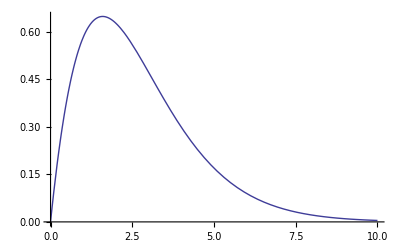

```mathematica
Clear[i]
i = Integrate[ x^2/(E^x-1), {x, 0, Infinity}]
i // N
Plot[x^2/(E^x-1),{x, 0, 10}, PlotRange -> Full]
```

```mathematica
peeters`exportForLatex["basicStatMechProblemSet7Problem1Fig1",basicStatMechProblemSet7Problem1Fig1]
```

{basicStatMechProblemSet7Problem1Fig1.eps,basicStatMechProblemSet7Problem1Fig1pn.png}